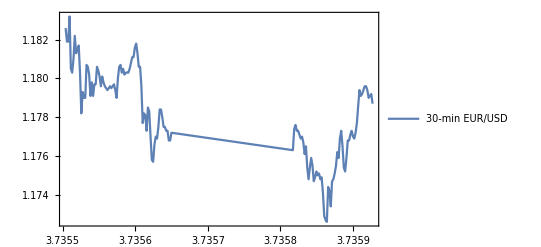

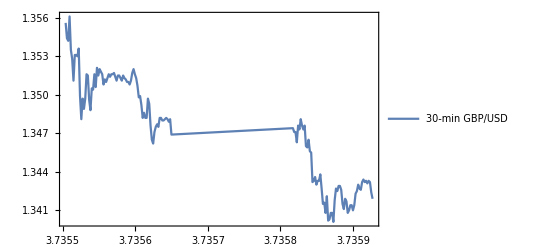

```mathematica
EURUSD=Import["/Users/wanghaibiao/Desktop/half-hour.xlsx",{"Data",1,Table[i,{i,2,145}],{1,3}}];
eurusd=Import["/Users/wanghaibiao/Desktop/half-hour.xlsx",{"Data",1,Table[i,{i,2,145}],3}];
GBPUSD=Import["/Users/wanghaibiao/Desktop/half-hour.xlsx",{"Data",1,Table[i,{i,2,145}],{1,2}}];
gbpusd=Import["/Users/wanghaibiao/Desktop/half-hour.xlsx",{"Data",1,Table[i,{i,2,145}],2}];
date=Import["/Users/wanghaibiao/Desktop/half-hour.xlsx",{"Data",1,Table[i,{i,2,145}],1}];
DateListPlot[EURUSD,PlotLegends->Placed[{"30-min EUR/USD"},Above]]
DateListPlot[GBPUSD,PlotLegends->Placed[{"30-min GBP/USD"},Above]]
```

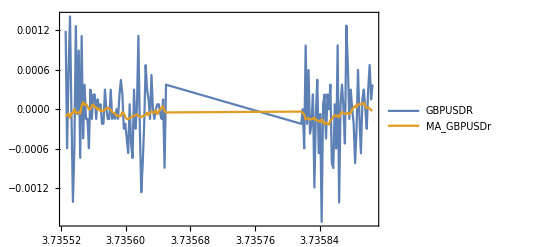

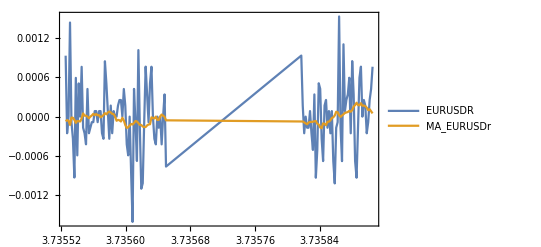

```mathematica
gbpusdr=Differences[Log[gbpusd]];
eurusdr=Differences[Log[eurusd]];
GBPUSDr=Table[{date[[i+12]],gbpusdr[[i+12]]},{i,1,120}];EURUSDr=Table[{date[[i+12]],eurusdr[[i+12]]},{i,1,120}];
mMAgbpusdr=MovingAverage[gbpusdr,24];
mMAeurusdr=MovingAverage[eurusdr,24];
mMAGBPUSDr=Table[{date[[i+12]],mMAgbpusdr[[i]]},{i,1,120}];mMAEURUSDr=Table[{date[[i+12]],mMAeurusdr[[i]]},{i,1,120}];
DateListPlot[{GBPUSDr,mMAGBPUSDr},PlotRange->{All,All},PlotLegends->Placed[{"GBPUSDR","MA_GBPUSDr"},Above]]
DateListPlot[{EURUSDr,mMAEURUSDr},PlotRange->{All,All},PlotLegends->Placed[{"EURUSDR","MA_EURUSDr"},Above]]
```

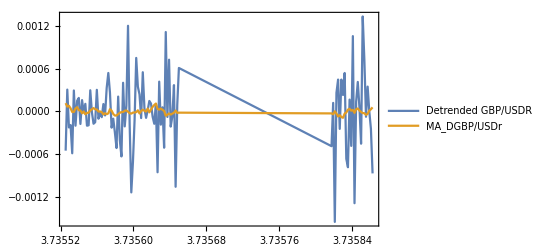

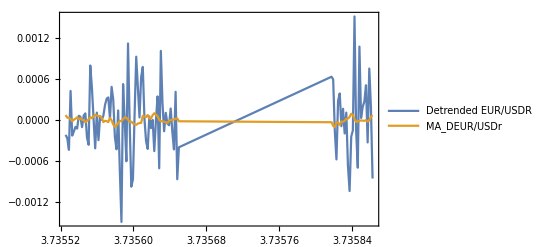

```mathematica
Dgbpusdr= Take[Drop[gbpusdr,12],120]-mMAgbpusdr;
Deurusdr= Take[Drop[eurusdr,12],120]-mMAeurusdr;
DGBPUSDr=Table[{date[[i+12]],Dgbpusdr[[i+12]]},{i,1,96}];
DEURUSDr=Table[{date[[i+12]],Deurusdr[[i+12]]},{i,1,96}];
mMADgbpusdr=MovingAverage[Dgbpusdr,24];
mMADeurusdr=MovingAverage[Deurusdr,24];
mMADGBPUSDr=Table[{date[[i+12]],mMADgbpusdr[[i]]},{i,1,96}];mMADEURUSDr=Table[{date[[i+12]],mMADeurusdr[[i]]},{i,1,96}];
DateListPlot[{DGBPUSDr,mMADGBPUSDr},PlotRange->{All,All},PlotLegends->Placed[{"Detrended GBP/USDR","MA_DGBP/USDr"},Above]]
DateListPlot[{DEURUSDr,mMADEURUSDr},PlotRange->All,PlotLegends->Placed[{"Detrended EUR/USDR","MA_DEUR/USDr"},Above]]
```

```mathematica
NSolve[m+theta==Mean[Dgbpusdr*100]&&sigma^2+theta^2==Variance[Dgbpusdr*100]&&(2*theta^3+3sigma^2*theta)/(sigma^2+theta^2)^1.5==Skewness[Dgbpusdr*100]&&sigma>0,{m,theta,sigma},Reals]
NSolve[m+theta==Mean[Deurusdr*100]&&sigma^2+theta^2==Variance[Deurusdr*100]&&(2*theta^3+3sigma^2*theta)/(sigma^2+theta^2)^1.5==Skewness[Deurusdr*100]&&sigma>0,{m,theta,sigma},Reals]
```

{{theta→0.00126047,sigma→0.0553631,m→0.00146005}}

{{theta→0.00314107,sigma→0.052153,m→-0.00101191}}

```mathematica
Subscript[θ, 1]=0.0012604731402425526;
Subscript[m, 1]=0.0014600547607820065;
Subscript[σ, 1]=0.0553631470722202;
Subscript[θ, 2]=0.003141074337581401;
Subscript[m, 2]=-0.001011913664099944;
Subscript[σ, 2]=0.05215295843843826;
```

```mathematica
F=Function[x,((2*Exp[Subscript[θ, 1]*(x-Subscript[m, 1])/Subscript[σ, 1]^2])/(Subscript[σ, 1]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m, 1])^2/(2*Subscript[σ, 1]^2+Subscript[θ, 1]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m, 1])^2*(2*Subscript[σ, 1]^2+Subscript[θ, 1]^2)]/Subscript[σ, 1]^2]][x]
```

12.7705 ⅇ^(0.411237 (-0.00146005+x)-25.5476 √((-0.00146005+x)^2)) (1+0./(√((-0.00146005+x)^2)))

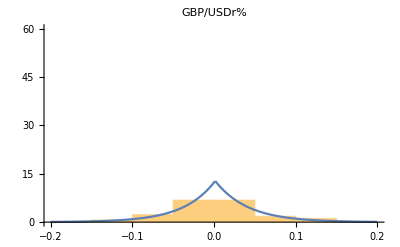

```mathematica
Show[Histogram[Dgbpusdr*100,Automatic,"ProbabilityDensity"],Plot[F,{x,-0.2,0.2},PlotRange->{Full,Full}],PlotRange->{All,{0,60}},PlotLabel->"GBP/USDr%"]
```

```mathematica
G=Function[x,((2*Exp[(Subscript[θ, 2])*(x-Subscript[m, 2])/Subscript[σ, 2]^2])/(Subscript[σ, 2]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m, 2])^2/(2*Subscript[σ, 2]^2+Subscript[θ, 2]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m, 2])^2*(2*Subscript[σ, 2]^2+Subscript[θ, 2]^2)]/Subscript[σ, 2]^2]][x]
```

13.546 ⅇ^(1.15484 (0.00101191+x)-27.1412 √((0.00101191+x)^2)) (1+0./(√((0.00101191+x)^2)))

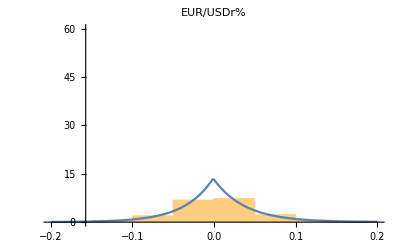

```mathematica
Show[Histogram[Deurusdr*100,Automatic,"ProbabilityDensity"],Plot[G,{x,-0.2,0.2},PlotRange->{Full,Full}],PlotRange->{All,{0,60}},PlotLabel->"EUR/USDr%"]
```

```mathematica
𝒟1=ProbabilityDistribution[F,{x,-Infinity,Infinity}];
DistributionFitTest[Dgbpusdr*100,𝒟1,"PearsonChiSquare"]
𝒟2=ProbabilityDistribution[G,{x,-Infinity,Infinity}];
DistributionFitTest[Deurusdr*100,𝒟2,"PearsonChiSquare"]
```

0.905554

0.73422

```mathematica
R12=Sin[Pi*KendallTau[Dgbpusdr*100,Deurusdr*100]/2];
R={{1,R12},{R12,1}};
MatrixForm[R]
```

(1 | 0.301286
0.301286 | 1)

```mathematica
L1=Dgbpusdr*100;
L2=Deurusdr*100;
data=Table[{L1[[i]],L2[[i]]},{i,1,120}];
```

```mathematica
EstimatedDistribution[data,CopulaDistribution[{"MultivariateT",R,v},{StudentTDistribution[v],StudentTDistribution[v]}],ParameterEstimator->"MaximumLikelihood"]
```

CopulaDistribution[{MultivariateT,{{1,0.301286},{0.301286,1}},30268.8},{StudentTDistribution[30268.8],StudentTDistribution[30268.8]}]

```mathematica
ν=30268.759831358715;
```

```mathematica
A=CholeskyDecomposition[R];
dist=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[ν]];
z1=RandomVariate[MarginalDistribution[dist,1],120];
z2=RandomVariate[MarginalDistribution[dist,2],120];
s=RandomVariate[MarginalDistribution[dist,3],120];
For[i=1,i≤120,i++,
Subscript[s, i]=s[[i]];
Subscript[y, i]=A.{z1[[i]],z2[[i]]};
Subscript[x, i]=Sqrt[ν]/Sqrt[Subscript[s, i]]*Subscript[y, i]];
x1=Table[Subscript[x, i][[1]],{i,120}];
x2=Table[Subscript[x, i][[2]],{i,120}];
Subscript[u, 1]=CDF[StudentTDistribution[ν],x1];
Subscript[u, 2]=CDF[StudentTDistribution[ν],x2];
```

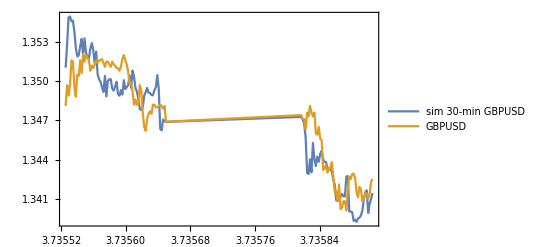

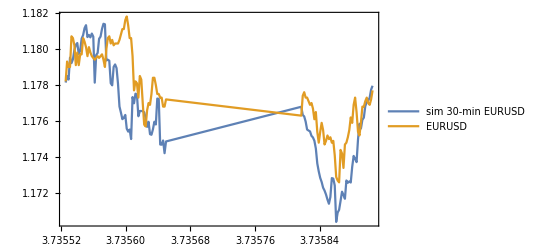

```mathematica
Subscript[Sim1, 0]=Take[Drop[gbpusd,11],1][[1]];
Subscript[Sim2, 0]=Take[Drop[eurusd,11],1][[1]];
S1=Take[Drop[gbpusd,12],120];
S2=Take[Drop[eurusd,12],120];
dates=Take[Drop[date,12],120];
Subscript[L, 1]=InverseCDF[𝒟1,Subscript[u, 1]];
Subscript[L, 2]=InverseCDF[𝒟2,Subscript[u, 2]];
For[t=1,t≤120,t++,
Subscript[L, 1,t]=Subscript[L, 1][[t]];
Subscript[L, 2,t]=Subscript[L, 2][[t]];
Subscript[Sim1, t]=Subscript[Sim1, t-1]*Exp[mMAgbpusdr[[t]]+Subscript[L, 1,t]/100];
Subscript[Sim2, t]=Subscript[Sim2, t-1]*Exp[mMAeurusdr[[t]]+Subscript[L, 2,t]/100]];
Sm1=Table[{dates[[t]],Subscript[Sim1, t]},{t,1,120}];
Sm2=Table[{dates[[t]],Subscript[Sim2, t]},{t,1,120}];
DateListPlot[{Sm1,Table[{dates[[t]],S1[[t]]},{t,1,120}]},PlotLegends->Placed[{"sim 30-min GBPUSD","GBPUSD"},Above]]
DateListPlot[{Sm2,Table[{dates[[t]],S2[[t]]},{t,1,120}]},PlotLegends->Placed[{"sim 30-min EURUSD","EURUSD"},Above]]
```